# Лабораторный практикум 7. Конформные отображения

Выполнила студентка ММФ БГУ
Вариант 2.
 1 к, 5 гр. Шклярик В.С.
 9 декабря 2021

## Задание 6.1-6.3 Функции для визуализации преобразования

Функция R2C, преобразовывает упорядоченную пару вещественных чисел {x,y}, представляющую координаты точки плоскости, в комплексное число в алгебраическом виде x+iy.
Функция C2R преобразовывает комплексное число в упорядоченную пару вещественных чисел {x,y}- координаты точки плоскости.

```mathematica
R2C[{x_,y_}]:=x+ⅈ y;
C2R[z_]:={Re@z,Im@z};
```

Функция TaskSubs[zz,f] генерирует графический образ заданного объекта zz в соответствии с заданной функцией f.
На входе: графический объект(прообраз),  функция комплексного переменного.
На выходе: отображение образа заданного графического объекта согласно заданной функции.

```mathematica
TaskSubs[zz_Graphics,f_]:=zz/.{Point[P_]:>(P//R2C//f//C2R//Point),(h:Line|Polygon)[P_]:>h[(#//R2C//f//C2R)&/@P]};
```

Функция ShowConform[f,g,opts] отображает объекты g и f[g] в режимах opts.
На входе: графический объект g, функция комплексного переменного f.
На выходе: графический объект g и его образ, полученный в результате применения правила f к g.

```mathematica
ClearAll[ShowConform];
ShowConform[f_,g_Graphics,opts___]:=Show[GraphicsGrid[{{g,TaskSubs[g,f]}}],opts]
```

## Задание 6.4 Полярная координатная сетка

```mathematica
Range[0,2π,π/4]
Range[0,1,.2]
```

{0,π/4,π/2,(3 π)/4,π,(5 π)/4,(3 π)/2,(7 π)/4,2 π}

{0.,0.2,0.4,0.6,0.8,1.}

```mathematica
Outer[#1{Cos[#2],Sin[#2]}&,Range[0,1,.2],Range[0,2π,π/4]];
```

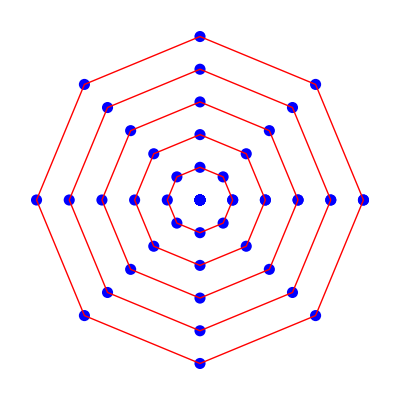

```mathematica
Graphics[{{Hue[2/3],PointSize[0.02],Map[Point,#1,{2}]},{Hue[0],Line/@#1}}&[Outer[#1{Cos[#2],Sin[#2]}&,Range[0,1,.2],Range[0,2π,π/4]]]]
```

Функция PolarMesh[r,{nr,nϕ}] строит графический объект для отображения  полярной координатной сетки радиуса от 0 до r. nr- количество линий, nϕ-количество узлов на каждой из линий.

```mathematica
PolarMesh[r_,{nr_,nϕ_}]:=({{Hue[2/3],PointSize[0.01],Map[Point,#1,{2}]},{Hue[0],Map[Line,#1,{1}]}}&)[Table[ρ{Cos[ϕ],Sin[ϕ]},{ρ,0,r,r/nr},{ϕ,0,2π,(2 π)/nϕ}]]
```

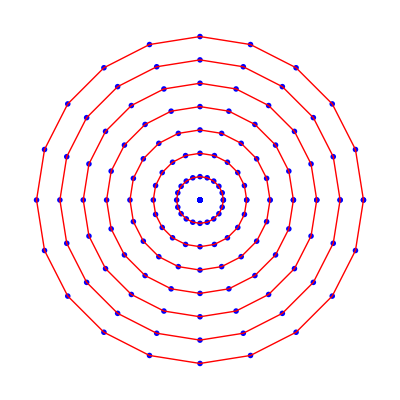

```mathematica
Graphics[PolarMesh[1,{7,20}]]
```

## Задание 6.10 Вариант 2.

Заданная область: часть кругового кольца 0<|z|<1, 0<arg z<π/2;
Функция: z → ⅇ^z.

```mathematica
Outer[#1{Cos[#2],Sin[#2]}&,Range[0,1,.1],Range[0,π/2,π/20]]//MatrixForm
```

((0.
0.) | (0.
0.) | (0.
0.) | (0.
0.) | (0.
0.) | (0.
0.) | (0.
0.) | (0.
0.) | (0.
0.) | (0.
0.) | (0.
0.)
(0.1
0.) | (0.0987688
0.0156434) | (0.0951057
0.0309017) | (0.0891007
0.045399) | (0.0809017
0.0587785) | (0.0707107
0.0707107) | (0.0587785
0.0809017) | (0.045399
0.0891007) | (0.0309017
0.0951057) | (0.0156434
0.0987688) | (0.
0.1)
(0.2
0.) | (0.197538
0.0312869) | (0.190211
0.0618034) | (0.178201
0.0907981) | (0.161803
0.117557) | (0.141421
0.141421) | (0.117557
0.161803) | (0.0907981
0.178201) | (0.0618034
0.190211) | (0.0312869
0.197538) | (0.
0.2)
(0.3
0.) | (0.296307
0.0469303) | (0.285317
0.0927051) | (0.267302
0.136197) | (0.242705
0.176336) | (0.212132
0.212132) | (0.176336
0.242705) | (0.136197
0.267302) | (0.0927051
0.285317) | (0.0469303
0.296307) | (0.
0.3)
(0.4
0.) | (0.395075
0.0625738) | (0.380423
0.123607) | (0.356403
0.181596) | (0.323607
0.235114) | (0.282843
0.282843) | (0.235114
0.323607) | (0.181596
0.356403) | (0.123607
0.380423) | (0.0625738
0.395075) | (0.
0.4)
(0.5
0.) | (0.493844
0.0782172) | (0.475528
0.154508) | (0.445503
0.226995) | (0.404508
0.293893) | (0.353553
0.353553) | (0.293893
0.404508) | (0.226995
0.445503) | (0.154508
0.475528) | (0.0782172
0.493844) | (0.
0.5)
(0.6
0.) | (0.592613
0.0938607) | (0.570634
0.18541) | (0.534604
0.272394) | (0.48541
0.352671) | (0.424264
0.424264) | (0.352671
0.48541) | (0.272394
0.534604) | (0.18541
0.570634) | (0.0938607
0.592613) | (0.
0.6)
(0.7
0.) | (0.691382
0.109504) | (0.66574
0.216312) | (0.623705
0.317793) | (0.566312
0.41145) | (0.494975
0.494975) | (0.41145
0.566312) | (0.317793
0.623705) | (0.216312
0.66574) | (0.109504
0.691382) | (0.
0.7)
(0.8
0.) | (0.790151
0.125148) | (0.760845
0.247214) | (0.712805
0.363192) | (0.647214
0.470228) | (0.565685
0.565685) | (0.470228
0.647214) | (0.363192
0.712805) | (0.247214
0.760845) | (0.125148
0.790151) | (0.
0.8)
(0.9
0.) | (0.88892
0.140791) | (0.855951
0.278115) | (0.801906
0.408591) | (0.728115
0.529007) | (0.636396
0.636396) | (0.529007
0.728115) | (0.408591
0.801906) | (0.278115
0.855951) | (0.140791
0.88892) | (0.
0.9)
(1.
0.) | (0.987688
0.156434) | (0.951057
0.309017) | (0.891007
0.45399) | (0.809017
0.587785) | (0.707107
0.707107) | (0.587785
0.809017) | (0.45399
0.891007) | (0.309017
0.951057) | (0.156434
0.987688) | (0.
1.))

```mathematica
grid=Outer[#1{Cos[#2],Sin[#2]}&,Range[0,1,.1],Range[0,π/2,π/20]];
```

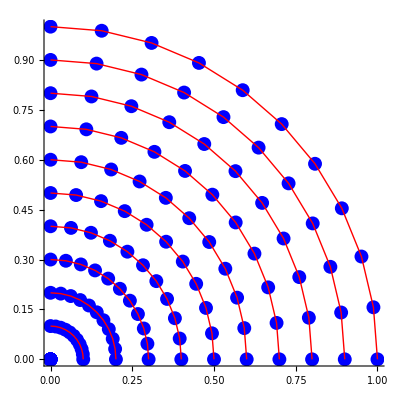

```mathematica
graphGrid=Graphics[({{Hue[2/3],PointSize[0.025],Map[Point,#1,{2}]},{Hue[0],Map[Line,#1,{1}]}}&)[grid],AspectRatio->Automatic,Axes->True]
```

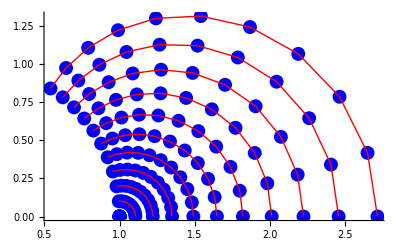

```mathematica
TaskSubs[graphGrid,ⅇ^#1&]
```

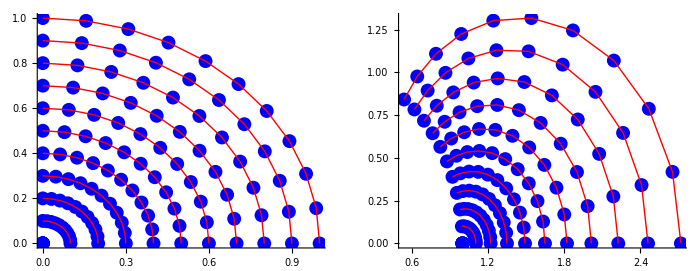

```mathematica
ShowConform[ⅇ^#1&,graphGrid,ImageSize->700,PlotLabel->(z↦ⅇ^z)]
```

## Отображение разноцветной полярной сетки

```mathematica
MapIndexed[f[#1,#2]&,{a,b,c}]
```

{f[a,{1}],f[b,{2}],f[c,{3}]}

```mathematica
MapIndexed[{Hue[((𝒩-#2⟦1⟧) 4/6+#2⟦1⟧ 3/6)/𝒩],Line[#1]}&,#]&;
```

Функция newPolarMesh[r0, r1, {nr,nϕ}, {ϕ0,ϕ1}] отображает разноцветную полярную координатную сетку радиуса от 0 до r. nr- количество линий, nϕ-количество узлов на каждой из линий. (ϕ0,ϕ1)-диапазон поворота полярного луча.

```mathematica
ClearAll[newPolarMesh];
newPolarMesh[r_,{nr_,nϕ_},{ϕ0_,ϕ1_}]:=Graphics[Module[{𝒩,grid=Outer[#1{Cos[#2],Sin[#2]}&,Range[0,r,r/nr],Range[ϕ0,ϕ1,ϕ1/nϕ]]},{𝒩=Length[grid];
MapIndexed[{Hue[((𝒩-#2⟦1⟧) 5/6+#2⟦1⟧ 3/6)/𝒩],PointSize[0.02],Point[#1]}&,grid,{2}],
MapIndexed[{Hue[((𝒩-#2⟦1⟧) 5/6+#2⟦1⟧ 3/6)/𝒩],Line[#1]}&,grid,{1}]}],Axes->True,AspectRatio->Automatic]
```

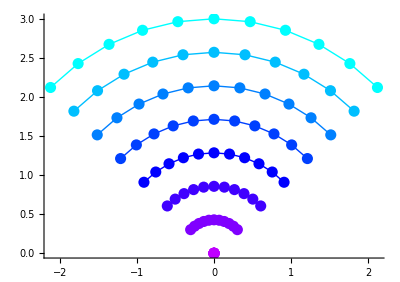

```mathematica
newPolarMesh[3,{7,15},{π/4,(3 π)/4}]
```

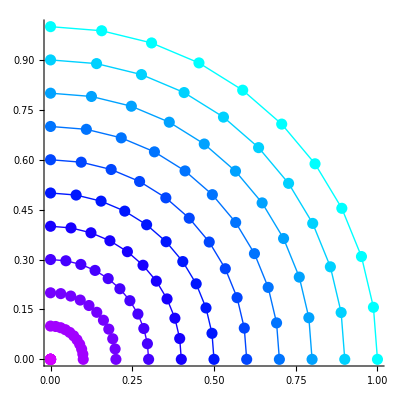

```mathematica
ClearAll[myPolarMesh];
myPolarMesh=newPolarMesh[1,{10,10},{0,π/2}]
```

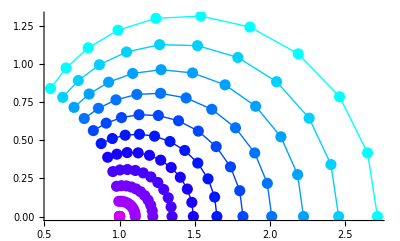

```mathematica
TaskSubs[myPolarMesh,ⅇ^#1&]
```

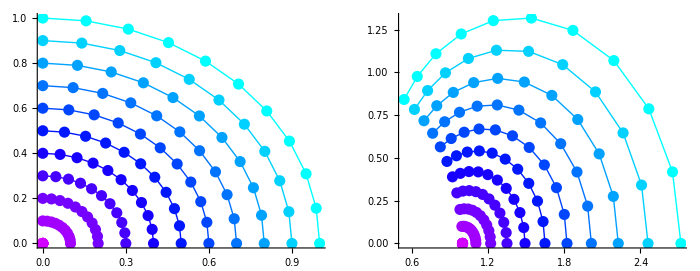

```mathematica
ShowConform[ⅇ^#1&,myPolarMesh,ImageSize->700,PlotLabel->(z↦ⅇ^z)]
```